## 空間内の球面の方程式

```mathematica
ctr={a,b,c};
rds=r;
({x,y,z}-ctr).({x,y,z}-ctr)==rds^2
```

(-a+x)^2+(-b+y)^2+(-c+z)^2==r^2

```mathematica
ctr={1,2,3};
rds=2;
ContourPlot3D[({x,y,z}-ctr).({x,y,z}-ctr)==rds^2,{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

◀     |     ▶

## 円周の媒介変数表示

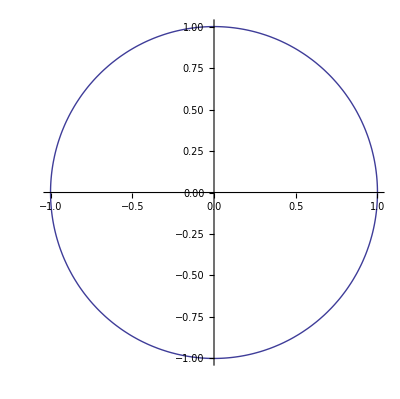

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

```mathematica
Manipulate[
Show[
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}],
Graphics[
{
{PointSize[Large],Point[{Cos[s],Sin[s]}]},
Line[{{0,0},{Cos[s],Sin[s]}}],
Circle[{0,0},1/6,{0,s}],
{Dashed,Line[{{Cos[s],0},{Cos[s],Sin[s]}}]},
{Dashed,Line[{{0,Sin[s]},{Cos[s],Sin[s]}}]}
}
]
],{{s,0,"角度"},0,2Pi},SaveDefinitions->True
]
```

◀     |     ▶

## 球面の媒介変数表示

```mathematica
ParametricPlot3D[{Cos[t]*Cos[s],Sin[t]*Cos[s],Sin[s]},{t,0,2Pi},{s,-Pi/2,Pi}]
```

-Graphics3D-

```mathematica
Manipulate[
Show[
Graphics3D[
{
Arrow[{{-1.4,0,0},{1.4,0,0}}],
Arrow[{{0,-1.4,0},{0,1.4,0}}],
Arrow[{{0,0,-1.4},{0,0,1.4}}],
{Thick,Line[{{0,0,0},{Cos[u]*Cos[v],Sin[u]*Cos[v],Sin[v]}}]},
{Dashed,Line[{{0,0,0},{Cos[u]*Cos[v],Sin[u]*Cos[v],0}}]},
{Dashed,Line[{{Cos[u]*Cos[v],Sin[u]*Cos[v],0},{Cos[u]*Cos[v],Sin[u]*Cos[v],Sin[v]}}]},
{PointSize[Large],Point[{Cos[u]*Cos[v],Sin[u]*Cos[v],Sin[v]}]}
}
],
ParametricPlot3D[{Cos[t]*Cos[s],Sin[t]*Cos[s],Sin[s]},{t,0,2Pi},{s,-Pi/2,Pi},Mesh->None,PlotStyle->Opacity[0.2]],
ParametricPlot3D[{Cos[u]*Cos[v],Sin[u]*Cos[v],Sin[v]},{u,0,2Pi}],
ParametricPlot3D[{Cos[u]*Cos[v],Sin[u]*Cos[v],Sin[v]},{v,-Pi/2,Pi/2}]
],{{u,Pi/8,"t：経度"},0,2Pi},{{v,Pi/6,"s：緯度"},-Pi/2,Pi/2},SaveDefinitions->True
]
```

◀     |     ▶